# PeerMind

## Statistical Quorum

### Code:

#### Simple/Super Majority

```mathematica
initializePopulation[size_,majority_:"simple"]:=(
(*majority ∈ {"simple","super","consensus"}.*)
populationSize=size;
voteType=majority;
)

createVotes[compressedVotes_]:=(
(*Takes in a list of {score,freq} pairs that it uncompresses into a list of actual votes.*)
Flatten[Table[
{score,freq}=item;
Table[If[score=="abstain","abstain",N[score]],{freq}]
,{item,compressedVotes}]]
)

computeVoteStatistics[votes_]:=(
(*Extracts required information from raw votes and stores them as global variables*)
abstentions=Count[votes,"abstain"];
effectivePopulationSize = populationSize-abstentions;
Which[
voteType=="simple",threshold=0.5*effectivePopulationSize,
voteType=="super",threshold=2./3*effectivePopulationSize,
voteType=="consensus",threshold=0.9*effectivePopulationSize
];
nonAbstentions=DeleteCases[votes,"abstain"];
numVoters=Length[nonAbstentions];
yes=Total[(nonAbstentions+1)/2];
no=numVoters-yes;
yesVotesNeeded=Ceiling[threshold-yes];
remainingVoters=effectivePopulationSize-numVoters;
{yes,no,yesVotesNeeded,remainingVoters}
)

computeCredibility[voteStatistics_]:=(
(*Computes the probability associated with the true bias in the population being greater than the necessary threshold to take action.*)
{yes,no,yesVotesNeeded,remainingVoters}=voteStatistics;
{a,b}={0.5,0.5};
(*{1,1} corresponds to a uniform prior, {0.5,0.5} correspnds to Jeffrey's prior.*)
prior[p_]:=PDF[BetaDistribution[yes+a,no+b],p];
credibility=Sum[Binomial[remainingVoters,numYes]*NIntegrate[p^(numYes)*(1-p)^(remainingVoters-numYes)*prior[p],{p,0,1}],{numYes,yesVotesNeeded,remainingVoters}];
credibility
)
```

#### Competing Motions

```mathematica
computeCompetingCredibility[voteStatistics_]:=(
(*Computes the probability that the first item's "yes-bias" is greater than that of all other items.*)
credibility=1;
{a,b}={0.5,0.5};
(*{1,1} corresponds to a uniform prior, {0.5,0.5} correspnds to Jeffrey's prior.*)
prior[p_,yes_,no_]:=PDF[BetaDistribution[yes+a,no+b],p];
{yes1,no1,yesVotesNeeded1,remainingVoters1}=voteStatistics[[1]];
Do[
{yesI,noI,yesVotesNeededI,remainingVotersI}=voteStatistics[[i]];
diff=Ceiling[yes1-yesI];
credibility*=1-Sum[
Binomial[remainingVoters1,numYes1]*Binomial[remainingVotersI,numYesI]*
NIntegrate[
p1^(numYes1)*(1-p1)^(remainingVoters1-numYes1)*
pI^(numYesI)*(1-pI)^(remainingVotersI-numYesI)*
prior[p1,yes1,no1]*prior[pI,yesI,noI]
,{p1,0,1},{pI,0,1}]
,{numYes1,0,remainingVoters1},{numYesI,diff+numYes1,remainingVotersI}];
,{i,2,Length[voteStatistics]}];
credibility
)
```

### Analysis:

```mathematica
ListPlot[
{samples[[All,2,2]],samples[[All,2,3]],samples[[All,2,4]],samples[[All,2,5]]},
FrameLabel->{"β","Complexity"},
PlotLegends->{"MI(X)","SI(X→X')","IF(X→X')","Φ_G"},
DataRange->{lower,upper},Joined->True,Filling->Axis,PlotRange->All,PlotStyle->Thick,
Frame->True,FrameStyle->Directive[Black,Thickness[Medium]],LabelStyle->{20},ImageSize->Large,AspectRatio->1]
```

#### Simple Majority

```mathematica
c=ParallelTable[
initializePopulation[100,"simple"];
votes=createVotes[{{1,i},{-1,10}}];
voteStatistics=computeVoteStatistics[votes];
{i,computeCredibility[voteStatistics]},{i,0,25}];
```

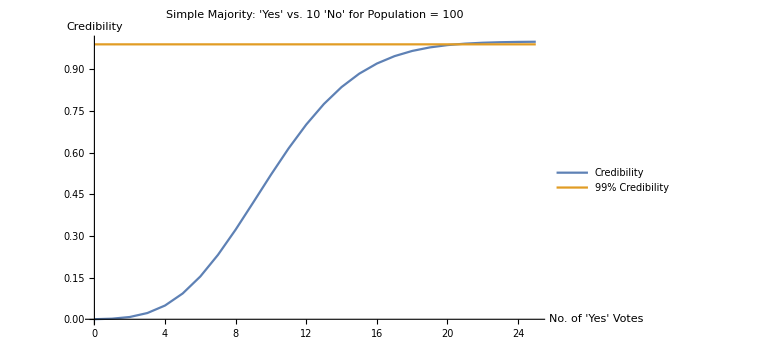

```mathematica
ListPlot[{c,Table[{i[[1]],0.99},{i,c}]},Joined->True,PlotLabel->"Simple Majority: 'Yes' vs. 10 'No' for Population = 100",AxesLabel->{"No. of 'Yes' Votes","Credibility"},PlotLegends->{"Credibility","99% Credibility"},ImageSize->Large]
```

#### Super Majority

```mathematica
c=ParallelTable[
initializePopulation[100,"super"];
votes=createVotes[{{1,i},{-1,10}}];
voteStatistics=computeVoteStatistics[votes];
{i,computeCredibility[voteStatistics]},{i,10,50}];
```

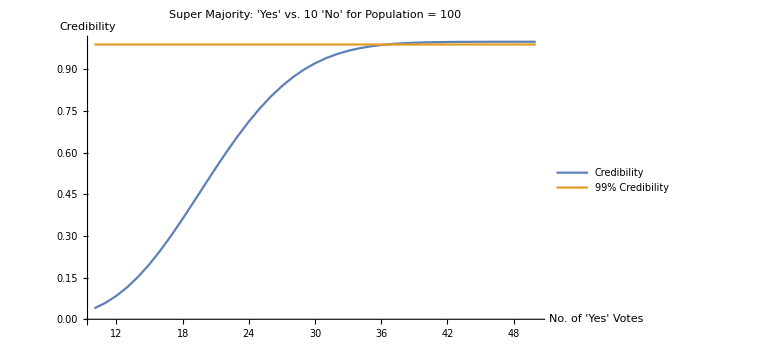

```mathematica
ListPlot[{c,Table[{i[[1]],0.99},{i,c}]},Joined->True,PlotLabel->"Super Majority: 'Yes' vs. 10 'No' for Population = 100",AxesLabel->{"No. of 'Yes' Votes","Credibility"},PlotLegends->{"Credibility","99% Credibility"},ImageSize->Large]
```

#### Competing Motions

```mathematica
initializePopulation[100,"simple"];
votes=Join[
{createVotes[{{1,99},{1,1}}]},
{createVotes[{{1,99},{0,0}}]}
];
voteStatistics=Table[computeVoteStatistics[v],{v,votes}];
computeCompetingCredibility[voteStatistics]
```

0.00990099

#### Individual Test Cases

```mathematica
initializePopulation[100,"simple"];
votes=createVotes[{{1,20},{-1,10},{"abstain",0}}];
voteStatistics=computeVoteStatistics[votes];
computeCredibility[voteStatistics]
```

0.988095

### To Do:

Incorporate higher-order statistics / perturbation theory to account for small sample sizes: Small perturbations in the votes of small samples can lead to drastically different levels of credibility, hence the overall credibility should be lowered/smoothed.

## Delegation [incomplete]

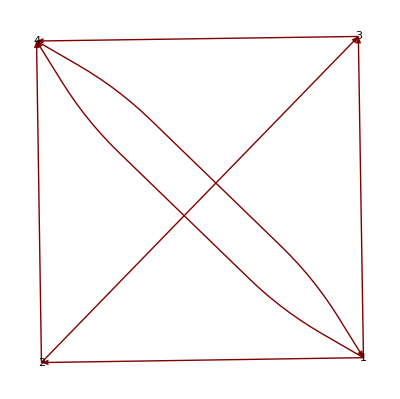

```mathematica
GraphPlot[{{1->2,.25},{2->3,.25},{2->4,.25},{3->4,.5},{1->3,.25},{4->1,.5},{1->4,.5}},VertexLabeling->True,DirectedEdges->True]
```

```mathematica
W={{1,0,0,0,0},{0.75,0,0,.25,0},{0,0,1,0,0},{0,.4,.4,0,.2},{0,0,0,0,0}}
```

{{1,0,0,0,0},{0.75,0,0,0.25,0},{0,0,1,0,0},{0,0.4,0.4,0,0.2},{0,0,0,0,0}}

```mathematica
v={0.7,0,-.4,0,0}
```

{0.7,0,-0.4,0,0}

```mathematica
W={{0,.25,.25,.5},{0,0,.25,.25},{0,0,0,.5},{.5,0,0,0}};W//MatrixForm
```

(0 | 0.25 | 0.25 | 0.5
0 | 0 | 0.25 | 0.25
0 | 0 | 0 | 0.5
0.5 | 0 | 0 | 0)

```mathematica
votes={-1,.5,0,0};
W=Join[Wᵀ,{votes}]ᵀ;W//MatrixForm
```

(0 | 0.25 | 0.25 | 0.5 | -1
0 | 0 | 0.25 | 0.25 | 0.5
0 | 0 | 0 | 0.5 | 0
0.5 | 0 | 0 | 0 | 0)

```mathematica
W=Join[W,{{0,0,0,0,1}}];W//MatrixForm
```

(0 | 0.25 | 0.25 | 0.5 | -1
0 | 0 | 0.25 | 0.25 | 0.5
0 | 0 | 0 | 0.5 | 0
0.5 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1)

```mathematica
votes=Join[votes,{0}]
```

{-1,0.5,0,0,0}

```mathematica
Eigensystem[W,1]//Chop
```

{{1.},{{-0.729243,0.130222,-0.182311,-0.364622,0.53391}}}

```mathematica
%[[2]]//MatrixForm
```

(-0.729243 | 0.130222 | -0.182311 | -0.364622 | 0.53391)

```mathematica
Mean[%ᵀ]
```

{-0.122409}

Ok I think this is the solution:

I will demonstrate how this works by a toy example:
x_1 = x_2
x_2 = 0.5 x_2 + 0.5 x_3
x_3 = x_4
x_4 = 0.25 x_1 + 0.25 x_2 + 0.25 x_3 + 0.25 x_4
where these equations describe how each voter x_i delegates their vote to the population (including to themselves).

Now set up the following matrix:
Let each row correspond to voter x_i, and each column correspond to their delegation weight, with one caveat.  That caveat is that, if the voter has delegated a portion of their vote to themselves, put that portion multiplied by their current vote (or 0 if they have not voted) in an extra column at the end of the matrix.  So the diagonal of the matrix should always be all zeros.  Finally, add one final row at the bottom that corresponds to all zeros, with a 1 in the last column.
So you get a 5x5 matrix that looks like this.

Now to do your iterative algorithm, we simply take this matrix and multiple it by the vector of inputted votes so far.
Let’s say x_1 has not voted, x_2 has voted -1, x_3 voted 1, x_4 voted 1. 
Then we make the vector (0, -1, 1, 1, 1) as our current state. (We have appended an extra 1 to make 5 total entries).

So what happens when we multiply the matrix by the current state? We get this. Notice that this is what you would get if you ran the iterative algorithm for one step.  We look at the first four entries: (-1, 0, 1, 1/4), which are all correct and take into account people who have already voted.  Also note that we replaced that last column in the matrix with the appropriate values based on the initial state votes.

So now instead of iteratively running the algorithm, there is a theoretical result that tells us that the convergent state will simply be the eigenvector of that 5x5 matrix that corresponds to eigenvalue = 1.  So we do this.  And our final result is that the votes are: (-0.5, -0.5, 0, 0).

The last row/column in the matrix and the last row in the state vector can be ignored when interpreting calculations — they are just for making dimensionality purposes.

Sound good?  I am not 100% sure yet if these matrices will have exactly one eigenvalue of 1; I think because we are replacing people who have not voted yet with a vote of “0” here, you will always get a unique solution.  If we chose to leave their vote as some “unknown”, then this will not be solvable in general I think.

You are right that my previous method allowed voters to delegate to others such that even if they vote, it may not count.  This was stupid, but I included it to keep things simple.  The better way to implement what I had proposed would be to just adjust so that if you see someone has already voted, then you ignore all of their delegation stuff and replace their row in the matrix with [0 ... 0 1]. (This was for when I said all diagonal elements are 0 and you add extra column to matrix corresponding to “self-delegation”.)

Also, for abstentions, 

Are you basically finding where a delegate has abstained, removing their % of vote, and then renormalizing?

So if x_1 = .5 x_2 + .5 x_3, and x_3=abstain, then x_1 = x_2?

And what happens if a vote cannot be determined by delegates?  Then they count as no vote, right? In my toy example, I replaced no vote with ‘0’, but that is not what you want to do b/c voting ‘0’ is not the same as not having voted yet, so this was the additional thing to tweak with my approach.

```mathematica
{{0,1,0,0,0*a},{0,0,1/2,0,1/2 b},{0,0,0,1,0*c},{1/4,1/4,1/4,0,1/4*d},{0,0,0,0,1}}//MatrixForm
```

{{0, 1, 0, 0, 0}, {0, 0, 1/2, 0, -1/2}, {0, 0, 0, 1, 0}, {1/4, 1/4, 1/4, 0, 1/4}, {0, 0, 0, 0, 1}}*{0, -1, 1, 1, 1}

Eigensystem[{{0, 1, 0, 0, 0}, {0, 0, 1/2, 0, -1/2}, {0, 0, 0, 1, 0}, {1/4, 1/4, 1/4, 0, 1/4}, {0, 0, 0, 0, 1}}]

## Online Platform UI/UX Features

Refining the user homepage:

Need to show simple statistic on how many motions the user has voted on of the total proposed over a specified duration.  This will be an important tool to eventually incentivize participation, e.g., if you don’t vote in 25% of motions (including via delegation) by the end of the semester, uncooperative fine; if you vote in 75%+ of motions, +1 hour bonus workshift.

“RSS / News” feed with notifications: What new comments/motions have been made since you last checked (like Facebook notifications)?  (Issue #163)

Allow members to suggest Pros/Cons to be vetted by moderators.  (Issue #164)

Personalized Discussion dashboard showing # of unread comments, statistical quorum confidence level, vote tally.

Sidebar to easily navigate through various discussions while viewing a single item (like in Mail app).

Admin organizational tools:

Label discussions under categories (e.g. use of space, mural, etc.).  All users should be able to label.  Admin should be able to assign specific council labels to when that discussion was finalized.

Searching archived motions by date/label/council.

Allow the ability to distinguish withdrawing a motion prematurely (with a note/comment explaining why) from simply closing it and causing it to fail.

Allow admins to setup an automated emailing service to users, which, at specified times, compiles and links to results/open motions (like a smart digest).

Other:

Auto-link URLs.

Directly replying to comments; notifying individuals via “@username”.

Live Voting section.

Active motions/discussions summary page to display on TV @ main entrance (integrated with calendar of events + general announcements).

Carefully check numerical precision when computing binomial sums: (n choose k) explodes and 0.5^k goes to 0 exponentially fast.  Might need to use fancy bounds/approximations for larger binomial sums (e.g. Stirling, or see p. 51 of turquoise notebook).